```mathematica
Numerical methods for Stochastic Differential Equations
```

```mathematica
β=0.3;
α=100;
σ=1;
aFun[t_,x_]:=-β(x-α)
bFun[t_,x_]:= σ √x
```

```mathematica
eulerMaruyama[t0_,x0_,a_,b_]:=Module[{x=x0,t=t0,t1,solution={x0}},t1=t;Do[t=t1;t1++;x=x+a[t,x]*(t1-t)+b[t,x]*RandomVariate[NormalDistribution[0,1]]*√(t1-t);AppendTo[solution,x],20];solution]
```

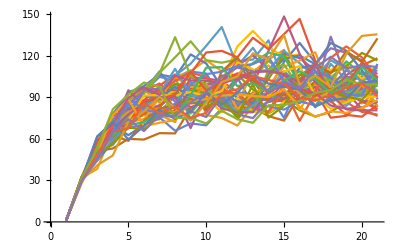

```mathematica
res=Table[eulerMaruyama[0,1,aFun,bFun],50];
ListLinePlot[res,PlotRange->{Automatic,Full}]
```

2 σ/(√(2β))- Ширина интервала сходимости процесса О-У.

```mathematica
2*σ/√(β*2)//N
```

3.87298

Runge-Kutt’s method

```mathematica
rungeKutt[t0_,x0_,a_,b_]:=Module[{x=x0,t=t0,t1,solution={x0},k1,k2,k3},t1=t;Do[t=t1;t1++;k1=x+a[t,x]*(t1-t)+b[t,x]*RandomVariate[NormalDistribution[0,1]]*√(t1-t);
k2=x+a[t,k1]*(t1-t)+b[t,k1]*√(t1-t);
k3=x+a[t,k2]*(t1-t)+b[t,k2]*√(t1-t);x=x+1/2(a[t,k1]+a[t,x])*(t1-t)+1/4(b[t,k2]+b[t,k3]+2b[t,x])*RandomVariate[NormalDistribution[0,1]]*√(t1-t)+1/4(b[t,k2]-b[t,k3])(RandomVariate[NormalDistribution[0,1]]*√(t1-t)-(t1-t))/√(t1-t);AppendTo[solution,x],20];solution]
```

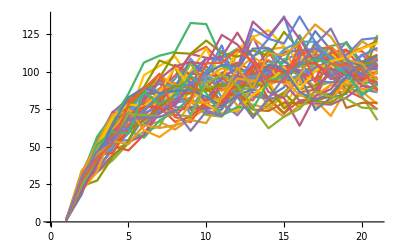

```mathematica
res2=Table[rungeKutt[0,1,aFun,bFun],50];
ListLinePlot[res2,PlotRange->{Automatic,Full}]
```